```mathematica
parse[s_]:=ToExpression@StringReplace[s,"e"->"*^"]
```

```mathematica
readq[file_]:=Module[{rawdata,xlow,step,data,nx},
rawdata=StringSplit/@StringSplit[Import[file],"\n"];
xlow=parse@rawdata[[4,1]];
step=parse@rawdata[[5,1]];
data=Map[parse,rawdata[[7;;]],{2}];
nx=Length@data;
<|
x->(Range@nx-1/2)*step+xlow,
h->data[[All,1]],
hu->data[[All,2]],
hv->data[[All,3]]
|>
]
readbath[file_]:=Module[{rawdata,xlow,step,data,nx},
rawdata=StringSplit/@StringSplit[Import[file],"\n"];
data=Map[parse,rawdata[[7;;]],{2}];
nx=Length@data;
data[[All,-1]]
]
```

```mathematica
bath=readbath["\\\\Ubuntu\\claw_results\\_output\\fort.ref.a0000"];
qRef1=readq["\\\\Ubuntu\\claw_results\\_output\\fort.ref.q0001"];
qRef2=readq["\\\\Ubuntu\\claw_results\\_output\\fort.ref.q0002"];
qRef5=readq["\\\\Ubuntu\\claw_results\\_output\\fort.ref.q0005"];
qRef10=readq["\\\\Ubuntu\\claw_results\\_output\\fort.ref.q0010"];
```

```mathematica
bathLow=readbath["\\\\Ubuntu\\claw_results\\_output\\fort.low.a0000"];
qUnb1=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qunb.q0001"];
qUnb2=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qunb.q0002"];
qUnb5=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qunb.q0005"];
qUnb10=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qunb.q0010"];
```

```mathematica
qLev1=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qlev.q0001"];
qLev2=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qlev.q0002"];
qLev5=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qlev.q0005"];
qLev10=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qlev.q0010"];
```

```mathematica
qRog1=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qrog.q0001"];
qRog2=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qrog.q0002"];
qRog5=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qrog.q0005"];
qRog10=readq["\\\\Ubuntu\\claw_results\\_output\\fort.qrog.q0010"];
```

```mathematica
qRogG1=readq["\\\\Ubuntu\\claw_results\\_output\\fort.q0001"];
qRogG2=readq["\\\\Ubuntu\\claw_results\\_output\\fort.q0002"];
qRogG5=readq["\\\\Ubuntu\\claw_results\\_output\\fort.q0005"];
qRogG10=readq["\\\\Ubuntu\\claw_results\\_output\\fort.q0010"];
```

-0.5

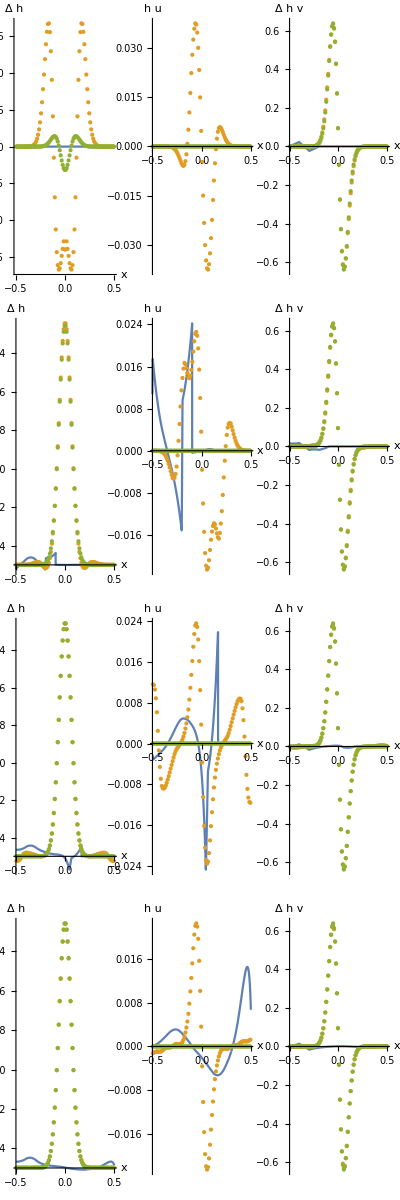

```mathematica
xlow=qRef[x][[1]]-(qRef[x][[2]]-qRef[x][[1]])/2
GraphicsGrid[#,ImageSize->1200]&/@List/@{
{
ListPlot[{Transpose[{qRef1[x],0qRef1[h]}],Transpose[{qUnb1[x],qUnb1[h]+bathLow-1-0.5Exp[-128qUnb1[x]^2]}],Transpose[{qLev1[x],qLev1[h]+bathLow-1-0.5Exp[-128qLev1[x]^2]}]},hOpts={AxesOrigin->{xlow,1},Joined->{True,False,False,False,False},PlotStyle->{,PointSize@Medium,PointSize@Medium,PointSize@Medium,PointSize@Medium},AxesLabel->{Style[x,Directive@14],Style[Δ h,Directive@14]},TicksStyle->Directive[14],PlotRange->All}],
ListPlot[{Transpose[{qRef1[x],0qRef1[hu]}],Transpose[{qUnb1[x],qUnb1[hu]}],Transpose[{qLev1[x],qLev1[hu]}]},huOpts={AxesOrigin->{xlow,0},Joined->{True,False,False,False,False},PlotStyle->{,PointSize@Medium,PointSize@Medium,PointSize@Medium,PointSize@Medium},AxesLabel->{Style[x,Directive@14],Style[h u,Directive@14]},TicksStyle->Directive[14],PlotRange->All}],
ListPlot[{Transpose[{qRef1[x],qRef1[hv]}],Transpose[{qUnb1[x],qUnb1[hv]}],Transpose[{qLev1[x],qLev1[hv]}]},hvOpts={AxesOrigin->{xlow,0},Joined->{True,False,False,False,False},PlotStyle->{,PointSize@Medium,PointSize@Medium,PointSize@Medium,PointSize@Medium},AxesLabel->{Style[x,Directive@14],Style[Δ h v,Directive@14]},TicksStyle->Directive[14],PlotRange->All}]
},
{
ListPlot[{Transpose[{qRef2[x],0qRef2[h]}],Transpose[{qUnb1[x],qUnb2[h]+bathLow-1-0.5Exp[-128qUnb1[x]^2]}],Transpose[{qLev2[x],qLev2[h]+bathLow-1-0.5Exp[-128qUnb1[x]^2]}]},hOpts],
ListPlot[{Transpose[{qRef2[x],qRef2[hu]}],Transpose[{qUnb1[x],qUnb2[hu]}],Transpose[{qLev2[x],qLev2[hu]}]},huOpts],
ListPlot[{Transpose[{qRef2[x],qRef2[hv]}],Transpose[{qUnb1[x],qUnb2[hv]}],Transpose[{qLev2[x],qLev2[hv]}]},hvOpts]
},
{
ListPlot[{Transpose[{qRef5[x],0qRef5[h]}],Transpose[{qUnb1[x],qUnb5[h]+bathLow-1-0.5Exp[-128qUnb1[x]^2]}],Transpose[{qLev5[x],qLev5[h]+bathLow-1-0.5Exp[-128qUnb1[x]^2]}]},hOpts],
ListPlot[{Transpose[{qRef5[x],qRef5[hu]}],Transpose[{qUnb1[x],qUnb5[hu]}],Transpose[{qLev5[x],qLev5[hu]}]},huOpts],
ListPlot[{Transpose[{qRef5[x],qRef5[hv]}],Transpose[{qUnb1[x],qUnb5[hv]}],Transpose[{qLev5[x],qLev5[hv]}]},hvOpts]
},
{
ListPlot[{Transpose[{qRef10[x],0qRef10[h]}],Transpose[{qUnb1[x],qUnb10[h]+bathLow-1-0.5Exp[-128qUnb1[x]^2]}],Transpose[{qLev10[x],qLev10[h]+bathLow-1-0.5Exp[-128qUnb1[x]^2]}]},hOpts],
ListPlot[{Transpose[{qRef10[x],qRef10[hu]}],Transpose[{qUnb1[x],qUnb10[hu]}],Transpose[{qLev10[x],qLev10[hu]}]},huOpts],
ListPlot[{Transpose[{qRef10[x],qRef10[hv]}],Transpose[{qUnb1[x],qUnb10[hv]}],Transpose[{qLev10[x],qLev10[hv]}]},hvOpts]
}
}//TableForm
```

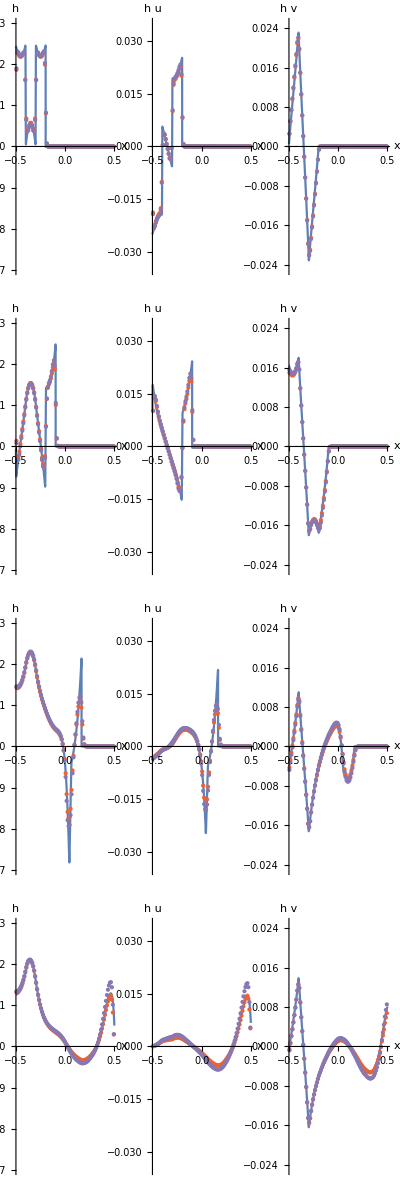

```mathematica
GraphicsGrid[#,ImageSize->1200]&/@List/@{
{
ListPlot[{Transpose[{qRef1[x],qRef1[h]+bath}],{{-10,0}},{{-10,0}},Transpose[{qRog1[x],qRog1[h]+1}],Transpose[{qRogG1[x],qRogG1[h]+1}]},hOpts={AxesOrigin->{xlow,1},Joined->{True,False,False,False,False},PlotStyle->{,PointSize@Medium,PointSize@Medium,PointSize@Medium,PointSize@Medium},AxesLabel->{Style[x,Directive@14],Style[h,Directive@14]},TicksStyle->Directive[14],PlotRange->{{-.5,.5},{0.97,1.03}}}],
ListPlot[{Transpose[{qRef1[x],qRef1[hu]}],{{-10,0}},{{-10,0}},Transpose[{qRog1[x],qRog1[hu]}],Transpose[{qRogG1[x],qRogG1[hu]}]},huOpts={AxesOrigin->{xlow,0},Joined->{True,False,False,False,False},PlotStyle->{,PointSize@Medium,PointSize@Medium,PointSize@Medium,PointSize@Medium},AxesLabel->{Style[x,Directive@14],Style[h u,Directive@14]},TicksStyle->Directive[14],PlotRange->{{-.5,.5},{-0.035,0.035}}}],
ListPlot[{Transpose[{qRef1[x],qRef1[hv]}],{{-10,0}},{{-10,0}},Transpose[{qRog1[x],qRog1[hv]}],Transpose[{qRogG1[x],qRogG1[hv]}]},hvOpts={AxesOrigin->{xlow,0},Joined->{True,False,False,False,False},PlotStyle->{,PointSize@Medium,PointSize@Medium,PointSize@Medium,PointSize@Medium},AxesLabel->{Style[x,Directive@14],Style[h v,Directive@14]},TicksStyle->Directive[14],PlotRange->{{-.5,.5},{-0.025,0.025}}}]
},
{
ListPlot[{Transpose[{qRef2[x],qRef2[h]+bath}],{{-10,0}},{{-10,0}},Transpose[{qRog2[x],qRog2[h]+1}],Transpose[{qRogG2[x],qRogG2[h]+1}]},hOpts],
ListPlot[{Transpose[{qRef2[x],qRef2[hu]}],{{-10,0}},{{-10,0}},Transpose[{qRog2[x],qRog2[hu]}],Transpose[{qRogG2[x],qRogG2[hu]}]},huOpts],
ListPlot[{Transpose[{qRef2[x],qRef2[hv]}],{{-10,0}},{{-10,0}},Transpose[{qRog2[x],qRog2[hv]}],Transpose[{qRogG2[x],qRogG2[hv]}]},hvOpts]
},
{
ListPlot[{Transpose[{qRef5[x],qRef5[h]+bath}],{{-10,0}},{{-10,0}},Transpose[{qRog5[x],qRog5[h]+1}],Transpose[{qRogG5[x],qRogG5[h]+1}]},hOpts],
ListPlot[{Transpose[{qRef5[x],qRef5[hu]}],{{-10,0}},{{-10,0}},Transpose[{qRog5[x],qRog5[hu]}],Transpose[{qRogG5[x],qRogG5[hu]}]},huOpts],
ListPlot[{Transpose[{qRef5[x],qRef5[hv]}],{{-10,0}},{{-10,0}},Transpose[{qRog5[x],qRog5[hv]}],Transpose[{qRogG5[x],qRogG5[hv]}]},hvOpts]
},
{
ListPlot[{Transpose[{qRef10[x],qRef10[h]+bath}],{{-10,0}},{{-10,0}},Transpose[{qRog10[x],qRog10[h]+1}],Transpose[{qRogG10[x],qRogG10[h]+1}]},hOpts],
ListPlot[{Transpose[{qRef10[x],qRef10[hu]}],{{-10,0}},{{-10,0}},Transpose[{qRog10[x],qRog10[hu]}],Transpose[{qRogG10[x],qRogG10[hu]}]},huOpts],
ListPlot[{Transpose[{qRef10[x],qRef10[hv]}],{{-10,0}},{{-10,0}},Transpose[{qRog10[x],qRog10[hv]}],Transpose[{qRogG10[x],qRogG10[hv]}]},hvOpts]
}
}//TableForm
```